{Ax-Ay+By,Ax+Ay-Bx}

{-Ay+Bx+By,Ax-Bx+By}

{Ax+Ay-By,-Ax+Ay+Bx}

{Ay+Bx-By,-Ax+Bx+By}

{1/2 (Ax+Ay+Bx-By),1/2 (-Ax+Ay+Bx+By)}

{1/2 (Ax-Ay+Bx+By),1/2 (Ax+Ay-Bx+By)}

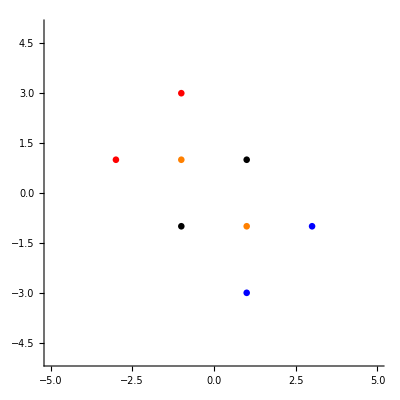

```mathematica
ClearAll["Global`*"];
nRad=.1;
pA={Ax,Ay};
pB={Bx,By};
pM={Mx,My}= {(Ax+Bx)/2,(Ay+By)/2};
pC={Cx,Cy};
pD={Dx,Dy};
vAB={Bx-Ax,By-Ay};
vBA={Ax-Bx,Ay-By};
rot[θ_]:=({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}});

pC1=vAB.rot[π/2]+pA
pD1=vBA.rot[-π/2]+pB

pC2=vAB.rot[-π/2]+pA
pD2=vBA.rot[π/2]+pB

vMA={Ax-Mx,Ay-My};
pC3=vMA.rot[π/2]+pM//Simplify
pD3=vMA.rot[-π/2]+pM//Simplify

(*{Ax,Ay}={1, 1};
{Bx,By}={1, 2};
{Cx,Cy}={2, 1};
{Dx,Dy}={2, 2};*)
{Ax,Ay}={1, 1};
{Bx,By}={-1,-1};
{Cx,Cy}={1,-1};
{Dx,Dy}={-1, 1};
dA=Graphics[{Black,Disk[pA,nRad]}];
dB=Graphics[{Black,Disk[pB,nRad]}];
dC1=Graphics[{Red,Disk[pC1,nRad]}];
dD1=Graphics[{Red,Disk[pD1,nRad]}];
dC2=Graphics[{Blue,Disk[pC2,nRad]}];
dD2=Graphics[{Blue,Disk[pD2,nRad]}];
dC3=Graphics[{Orange,Disk[pC3,nRad]}];
dD3=Graphics[{Orange,Disk[pD3,nRad]}];

dC=Graphics[{Black,Disk[pC,nRad]}];
dD=Graphics[{Black,Disk[pD,nRad]}];
Show[
dA,dB,
dC1,dD1,
dC2,dD2,
dC3,dD3,
Axes->True,
AspectRatio->Automatic,
PlotRange->{{-5,5},{-5,5}}
]
```